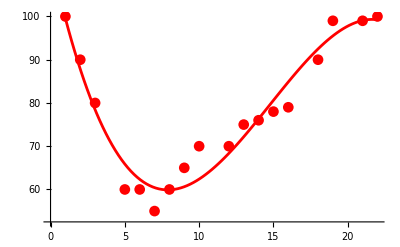

```mathematica
xData={1,2,3,5,6,7,8,9,10,12,13,14,15,16,18,19,21,22};
yData={100,90,80,60,60,55,60,65,70,70,75,76,78,79,90,99,99,100};


model=Fit[Transpose[{xData,yData}],{1,x,x^2,x^3},x];


xLine=Subdivide[1,22,100];
yLine=model /. x-># & /@ xLine;


Show[
    ListPlot[Transpose[{xData,yData}],PlotStyle->Red,PlotMarkers->Automatic],
    ListLinePlot[Transpose[{xLine,yLine}],PlotStyle->Red]
]
```

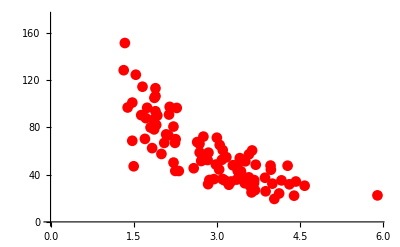

```mathematica
SeedRandom[2]; 

x=RandomVariate[NormalDistribution[3,1],100];
y=RandomVariate[NormalDistribution[150,40],100]/x;

ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotMarkers->Automatic]
```

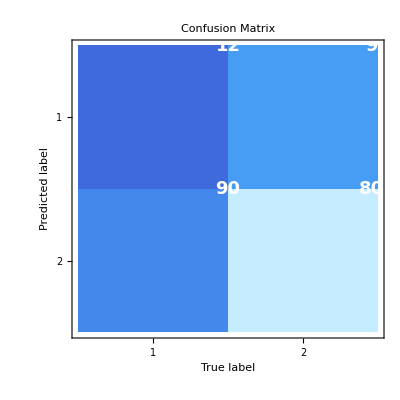

```mathematica
confusionMatrix={{12,93},{90,805}};

MatrixPlot[
    confusionMatrix,
    ColorFunction->"DeepSeaColors",
    FrameTicks->{{Automatic,None},{Automatic,None}},
    FrameLabel->{"Predicted label","True label"},
    FrameStyle->Directive[Bold,White],
    PlotLabel->Style["Confusion Matrix",Bold,14],
    AspectRatio->1,
    ColorFunctionScaling->True,
    Epilog->{
        Inset[Style[Text[confusionMatrix[[1,1]]],Bold,FontSize->18,White],{1,2}],
        Inset[Style[Text[confusionMatrix[[1,2]]],Bold,FontSize->18,White],{2,2}],
        Inset[Style[Text[confusionMatrix[[2,1]]],Bold,FontSize->18,White],{1,1}],
        Inset[Style[Text[confusionMatrix[[2,2]]],Bold,FontSize->18,White],{2,1}]
    }
]
```

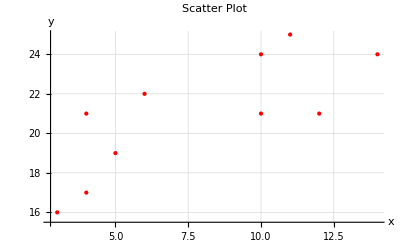

```mathematica
x={4,5,10,4,3,11,14,6,10,12};
y={21,19,24,17,16,25,24,22,21,21};

ListPlot[Transpose[{x,y}],PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"x","y"},PlotLabel->"Scatter Plot",GridLines->Automatic]
```

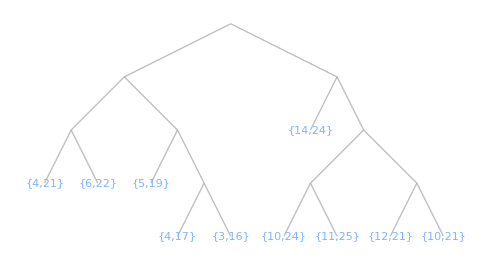
DendrogramPlot[-Graphics-,Orientation→Top,Method→Ward,Frame→True,FrameTicks→{{Automatic,None},{Automatic,None}},FrameLabel→{Index,Height},PlotRange→All,AspectRatio→1/2]

```mathematica
x={4,5,10,4,3,11,14,6,10,12};
y={21,19,24,17,16,25,24,22,21,21};

data=Transpose[{x,y}];

hc=ClusteringTree[data,DistanceFunction->EuclideanDistance];

DendrogramPlot[hc,
    Orientation->Top,
    Method->"Ward",
    Frame->True,
    FrameTicks->{{Automatic,None},{Automatic,None}},
    FrameLabel->{"Index","Height"},
    PlotRange->All,
    AspectRatio->1/2]
```

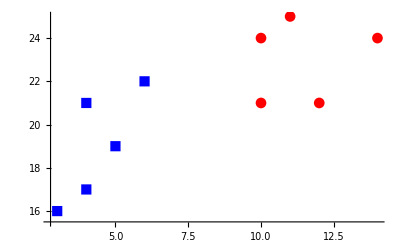

```mathematica
x={4,5,10,4,3,11,14,6,10,12};
y={21,19,24,17,16,25,24,22,21,21};

data=Transpose[{x,y}];

hc=FindClusters[data,UpTo[2],DistanceFunction->EuclideanDistance,
  Method->"Agglomerate"];

ListPlot[hc,PlotStyle->{Red,Blue},PlotMarkers->Automatic]
```

```mathematica
X={3.78,2.44,2.09,0.14,1.72,1.65,4.92,4.37,4.96,4.52,3.69,5.88};
y={0,0,0,0,0,0,1,1,1,1,1,1};

logr=Classify[Thread[X->y],Method->"LogisticRegression"];

predicted=logr[3.46]

probability=logr[3.46,"Probabilities"]
```

1

<|0→0.490179,1→0.509821|>

```mathematica
X={3.78,2.44,2.09,0.14,1.72,1.65,4.92,4.37,4.96,4.52,3.69,5.88};
y={0,0,0,0,0,0,1,1,1,1,1,1};

logr=Classify[Thread[X->y],Method->"LogisticRegression"];

lm=LogitModelFit[Transpose[{X,y}],x,x];

logOdds=lm["BestFitParameters"][[2]];

odds=Exp[logOdds]

{logOdds,odds}
```

LogitModelFit::dpbss: The number of unique basis functions is 9 fewer than the number of basis functions specified in {4,5,10,4,3,11,14,6,10,12}. Duplicated basis functions will be removed.

LogitModelFit::ivar: {4,5,10,4,3,11,14,6,10,12} is not a valid variable.

Part::partw: Part 2 of LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12},{4,5,10,4,3,11,14,6,10,12}][BestFitParameters] does not exist.

ⅇ^(LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12},{4,5,10,4,3,11,14,6,10,12}][BestFitParameters]⟦2⟧)

{LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12},{4,5,10,4,3,11,14,6,10,12}][BestFitParameters]⟦2⟧,ⅇ^(LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12},{4,5,10,4,3,11,14,6,10,12}][BestFitParameters]⟦2⟧)}

```mathematica
X={3.78,2.44,2.09,0.14,1.72,1.65,4.92,4.37,4.96,4.52,3.69,5.88};
y={0,0,0,0,0,0,1,1,1,1,1,1};

logr=LogitModelFit[Transpose[{X,y}],x];

probabilities=logr["ProbabilityFunction"] /@ X

probabilities
```

{LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][3.78],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][2.44],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][2.09],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][0.14],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][1.72],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][1.65],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.92],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.37],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.96],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.52],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][3.69],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][5.88]}

{LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][3.78],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][2.44],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][2.09],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][0.14],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][1.72],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][1.65],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.92],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.37],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.96],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][4.52],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][3.69],LogitModelFit[{{3.78,0},{2.44,0},{2.09,0},{0.14,0},{1.72,0},{1.65,0},{4.92,1},{4.37,1},{4.96,1},{4.52,1},{3.69,1},{5.88,1}},{4,5,10,4,3,11,14,6,10,12}][ProbabilityFunction][5.88]}

```mathematica
iris=ExampleData["Dataset"];
X=iris[[All,1;;4]];
y=iris[[All,5]];

CList={0.25,0.5,0.75,1,1.25,1.5,1.75,2};

scoreForC[c_]:=Module[{model,accuracy},model=Classify[Thread[X->y],Method->{"LogisticRegression","RegularizationStrength"->c}];
accuracy=Mean[MapThread[Equal,{model/@X,y}]];
accuracy]

scores=scoreForC/@CList

scores
```

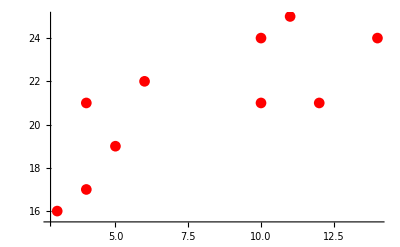

```mathematica
x={4,5,10,4,3,11,14,6,10,12};
y={21,19,24,17,16,25,24,22,21,21};


ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotMarkers->Automatic]
```

Thread::tdlen: Objects of unequal length in {{4,21},{5,19},{10,24},{4,17},{3,16},{11,25},{14,24},{6,22},{10,21},{12,21}}+{{-79/10,-21}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{4,21},{5,19},{10,24},{4,17},{3,16},{11,25},{14,24},{6,22},{10,21},{12,21}}+{{-57/5,-23},{-22/5,-19}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{4,21},{5,19},{10,24},{4,17},{3,16},{11,25},{14,24},{6,22},{10,21},{12,21}}+{{-57/5,-23},{-4,-52/3},{-5,-43/2}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

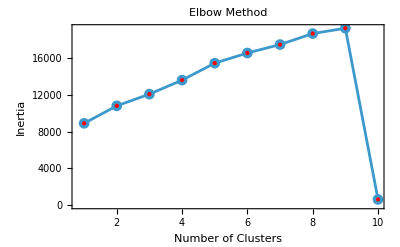

```mathematica
x={4,5,10,4,3,11,14,6,10,12};
y={21,19,24,17,16,25,24,22,21,21};

data=Transpose[{x,y}];

inertias=Table[
  Total[Map[Norm,data-(Mean /@ FindClusters[data,i])]^2],
  {i,1,10}
];

ListLinePlot[inertias,
 Frame->True,
 FrameLabel->{"Number of Clusters","Inertia"},
 PlotMarkers->Automatic,
 PlotRange->All,
 Epilog->{Red,PointSize[Medium],Point[Transpose[{Range[1,10],inertias}]]},
 PlotLabel->"Elbow Method"]
```